```mathematica
1/L Integrate[Abs[x],{x,-L,L}]
```

Abs[L]

```mathematica
ser[n_]:=1/π FourierSeries[x,x,n]/.x->π x;
ser2[n_]:=1/π FourierSeries[Abs[x],x,n]/.x->π x;
```

General::munfl: Exp[-799.438] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1194.22] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1667.96] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

{0.5-0.301419 Cos[π x],0.5-0.367195 Cos[π x]}

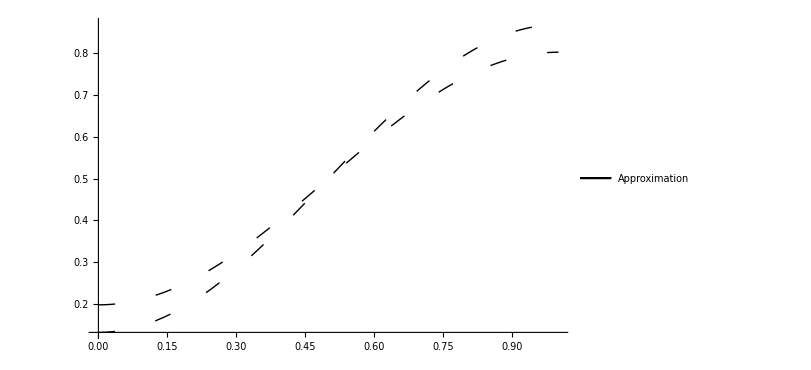

-Graphics-x/Lu(x,t)/L

/home/lmackay/Documents/256/2022W2/LM Notes/images/zero_flux_BCs_long_term.pdf

{RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179]}

{0.985,0.99,0.995,1.}

```mathematica
xzoom=.9999;
coeff=FourierCoefficient[Abs[x],x,n];
lbls = Evaluate[Style[#,FontSize->24]&/@{"x/L",Rotate["u(x,t)/L",π/2]}];
ser3[m_]:=1/2+Total[Table[Exp[-0.1((n π)/L)^2 t]coeff Cos[(n π)/L x],{n,1,m}]/(π/2)]
ser3[8000]/.{L->1};

Join[{x},%/.t->{.1,.3, 10}];
p1=Plot[%,{x,0,1},PlotStyle->Thick,PlotLabels->Evaluate[Style[#,FontSize->16]&/@{"t=0","t=0.05","t=0.3","t=10"}],ImageSize->{600,300},TicksStyle->Directive[FontSize->14]]
{%%[[3]][[1;;2]],%%[[2]][[1;;2]]}
p2=Plot[%,{x,0,1},PlotStyle->Directive[Dashing[{0.02, 0.05}],Black, Thick],ImageSize->{600,300},TicksStyle->Directive[FontSize->14],PlotLegends->Placed[LineLegend[{Black},Style[#,FontSize->18]&/@{"Approximation"}],{.35,.75}]]
(*p2=Labeled[Plot[Evaluate[%%[[1;;2]]],{x,xzoom,1},PlotStyle->Thick,PlotLabels->Evaluate[Style[#,FontSize->16]&/@{"t=0 (slope=1)","t=0.00001 (slope=0)"}],ImageSize->{600,300},AspectRatio->1,TicksStyle->Directive[FontSize->14], Ticks->Evaluate[{Subdivide[xzoom,1,3],Automatic}]],lbls,{Bottom,Left}];
Grid[{{p1,p2}}]*)
Labeled[Show[p1,p2],lbls,{Bottom,Left}]
Export[NotebookDirectory[]<>"zero_flux_BCs_long_term.pdf",%]
```

```mathematica
coeff2
```

-(2 (-1)^n)/n

```mathematica
Evaluate[{Subdivide[.985,1,3],Automatic}]
```

{{0.985,0.99,0.995,1.},Automatic}

{Directive[RGBColor[0.922526, 0.385626, 0.209179],Thickness[Large]],Directive[RGBColor[0.528488, 0.470624, 0.701351],Thickness[Large]]}

General::munfl: Exp[-719.494] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-773.777] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-830.034] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: -9.86926×10^-308 0.0540118 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-x/Lu(x,t)/L

-Graphics-

{0.+0.237273 Sin[π x],0.+0.388655 Sin[π x]}

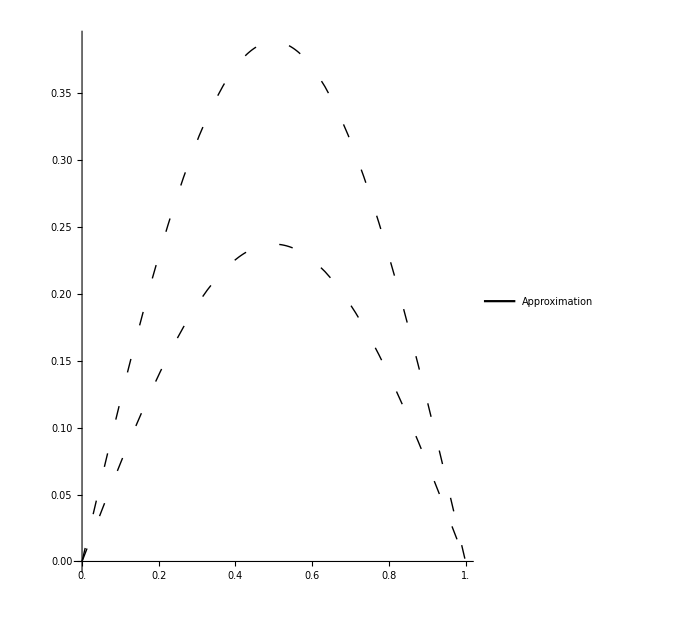

-Graphics-

-Graphics-x/Lu(x,t)/L | -Graphics-

/home/lmackay/Documents/256/2022W2/LM Notes/images/clamped_BCs_long_term.pdf

```mathematica
coeff2=FourierSinCoefficient[x,x,n];
lbls = Evaluate[Style[#,FontSize->16]&/@{"x/L",Rotate["u(x,t)/L",π/2]}];
ser4[m_]:=Total[Table[Exp[-0.1*((n π)/L)^2 t]coeff2 Sin[(n π)/L x],{n,1,m}]/π]
style=Directive[#,Thick]&/@(ColorData[97,"ColorList"][[4;;5]])
xzoom=.985;
ser4[1600]/.{L->1};
Join[{x},%/.t->{0.001,.1,.5,1}];
p1=Labeled[Plot[%,{x,0,1},PlotStyle->Thick,PlotLabels->Evaluate[Style[#,FontSize->24]&/@{"t=0","t=0.001","t=1","t=0.5"}],ImageSize->{600,300},TicksStyle->Directive[FontSize->14], PlotRange->{0.00001, 1}],lbls,{Bottom,Left}]

p2=Plot[Evaluate[%%[[4;;5]]],{x,0,1},PlotStyle->style,PlotLabels->Evaluate[Style[#,FontSize->16]&/@{"t=0.5","t=1"}],ImageSize->{500,300},AspectRatio->1,TicksStyle->Directive[FontSize->14],Ticks->Evaluate[{Subdivide[0,1,5]//N,Automatic}]]
{%%%[[5]][[1;;2]],%%%[[4]][[1;;2]]}

p3=Plot[%,{x,0,1},PlotStyle->Directive[Dashing[{0.02, 0.05}],Black, Thick],ImageSize->{500,300},AspectRatio->1.25,TicksStyle->Directive[FontSize->14],Ticks->Evaluate[{Subdivide[0,1,5]//N,Automatic}],PlotLegends->Placed[LineLegend[{Black},Style[#,FontSize->18]&/@{"Approximation"}],{.5,.35}]]
Show[p2,p3]
Grid[{{p1,%}}]
Export[NotebookDirectory[]<>"clamped_BCs_long_term.pdf",%]
```

```mathematica
HeavisideTheta[-1]
```

0

-HeavisideTheta[-3/4+x]+HeavisideTheta[-1/4+x]

{Directive[RGBColor[0.922526, 0.385626, 0.209179],Thickness[Large]],Directive[RGBColor[0.528488, 0.470624, 0.701351],Thickness[Large]]}

General::munfl: Exp[-712.585] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-870.499] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1044.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: -2.64265×10^-308 0.0540759 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

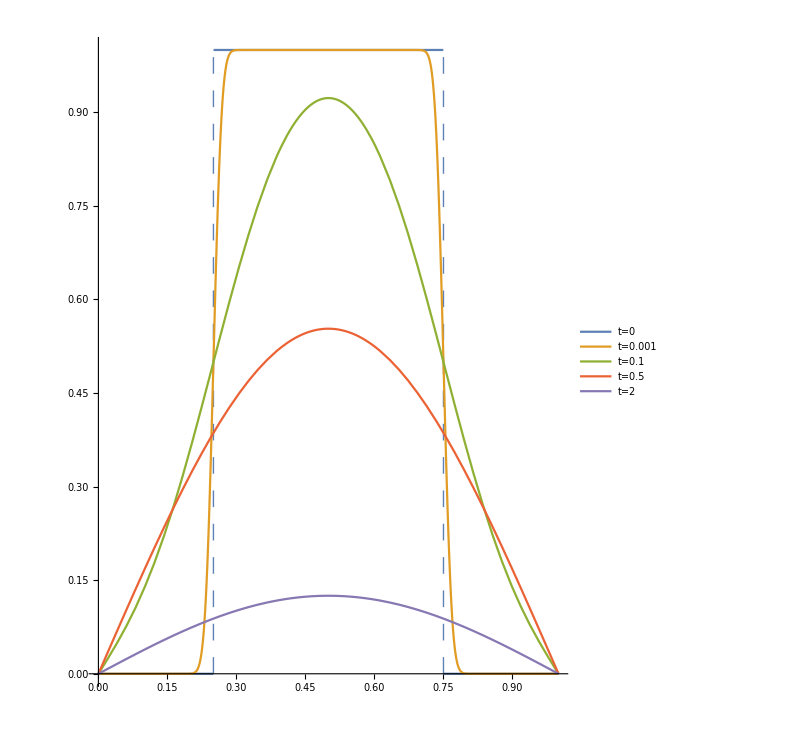
-Graphics-x/Lu(x,t)

/home/lmackay/Documents/256/2022W2/LM Notes/images/clamped_BCs_heaviside.pdf

```mathematica
u0=HeavisideTheta[x-1/4]-HeavisideTheta[x-3/4]
coeff2=π*FourierSinCoefficient[u0/.x->x/ π,x,n];
lbls = Evaluate[Style[#,FontSize->24]&/@{"x/L",Rotate["u(x,t)",π/2]}];
ser4[m_]:=Total[Table[Exp[-0.1((n π)/L)^2 t]coeff2 Sin[(n π)/L x],{n,1,m}]/π]
style=Directive[#,Thick]&/@(ColorData[97,"ColorList"][[4;;5]])
xzoom=.985;
ser4[1600]/.{L->1};
Join[{u0},%*(1-HeavisideTheta[x-1])/.t->{0.001,0.1,0.5,2}];
p1=Labeled[Plot[%,{x,0,1},PlotStyle->Thick,PlotLegends->Placed[Evaluate[Style[#,FontSize->24]&/@{"t=0","t=0.001","t=0.1","t=0.5","t=2"}],{.9,.5}],ImageSize->{600,600}, AspectRatio->1.25,TicksStyle->Directive[FontSize->14], PlotRange->Full, Prolog->{Directive[RGBColor[0.368417, 0.506779, 0.709798],Dashing[{0.02}], Thick],Line[{{1/4,0},{1/4,1}}],Line[{{3/4,0},{3/4,1}}]}],lbls,{Bottom,Left}]

Export[NotebookDirectory[]<>"clamped_BCs_heaviside.pdf",%]
```

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

-HeavisideTheta[-3/4+x]+HeavisideTheta[-1/4+x]

ConditionalExpression[((3-4 L) HeavisideTheta[-3/4+L]+(-1+4 L) HeavisideTheta[-1/4+L])/(2 L), L∈ℝ]

{Directive[RGBColor[0.922526, 0.385626, 0.209179],Thickness[Large]],Directive[RGBColor[0.528488, 0.470624, 0.701351],Thickness[Large]]}

General::munfl: Exp[-888.264] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1140.93] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1425.17] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

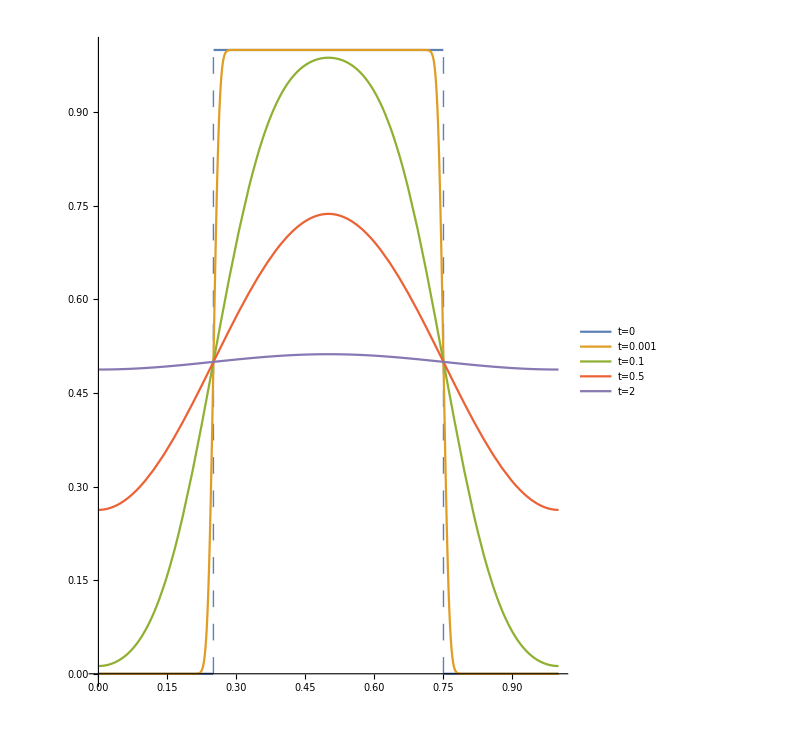
-Graphics-x/Lu(x,t)/L

/home/lmackay/Documents/256/2022W2/LM Notes/images/zero_flux_BCs_heaviside.pdf

```mathematica
u0=HeavisideTheta[x-1/4]-HeavisideTheta[x-3/4]
coeff2=π*FourierCosCoefficient[u0/.x->x/ π,x,n];
a0=2/L Integrate[u0,{x,0,L}]
lbls = Evaluate[Style[#,FontSize->24]&/@{"x/L",Rotate["u(x,t)/L",π/2]}];
ser4[m_]:=a0/2+Total[Table[Exp[-0.05((n π)/L)^2 t]coeff2 Cos[(n π)/L x],{n,1,m}]/π]
style=Directive[#,Thick]&/@(ColorData[97,"ColorList"][[4;;5]])
xzoom=.985;
ser4[1600]/.{L->1};
Join[{u0},%*(1-HeavisideTheta[x-1])/.t->{0.001,0.1,.5,2}];
p1=Labeled[Plot[%,{x,0,1},PlotStyle->Thick,PlotLegends->Placed[Evaluate[Style[#,FontSize->24]&/@{"t=0","t=0.001","t=0.1","t=0.5","t=2"}],{.9,.75}],ImageSize->{600,600},ImageSize->{600,600}, AspectRatio->1.25,TicksStyle->Directive[FontSize->14], PlotRange->Full, Prolog->{Directive[RGBColor[0.368417, 0.506779, 0.709798],Dashing[{0.02}], Thick],Line[{{1/4,0},{1/4,1}}],Line[{{3/4,0},{3/4,1}}]}],lbls,{Bottom,Left}]

Export[NotebookDirectory[]<>"zero_flux_BCs_heaviside.pdf",%]
```

```mathematica
ser200=ser[200];
ser2000=ser[2000];
ser4=ser[4];
```

$Aborted

$Aborted

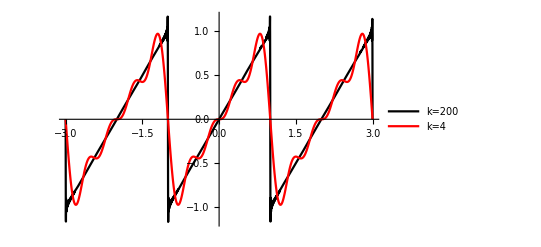

sawtooth_series.pdf

/home/lmackay/Documents/256/2022W1/LM Notes/images/wtv

```mathematica
Plot[Evaluate[{ser200, ser4}],{x,-3,3},PlotStyle->{Black, Red},PlotLegends->{"k=200","k=4"}]
Export[NotebookDirectory[]<>"sawtooth_series.pdf",%]
```

```mathematica
-1/(100*π^2)Log[π^3/64]//N
```

0.000734268

```mathematica
-1/(0.4*π^2)Log[(0.01 π^2)/6]//N
```

1.04043

```mathematica
Piecewise[{{x<1,x}}]
```

Piecewise[{{x<1, x}, {0, True}}]

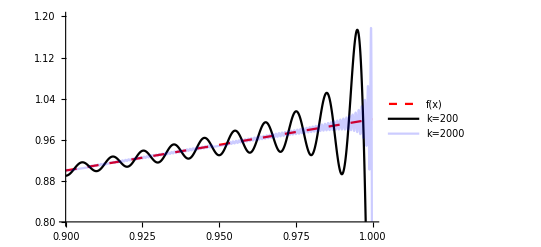

/home/lmackay/Documents/256/2022W1/LM Notes/images/sawtooth_zoom_in.pdf

```mathematica
Plot[{Piecewise[{{x,x<1}}],ser200,ser2000},{x,.9,1},PlotStyle->{Directive[Red, Dashing[{.02,.02}]],Black, Directive[Blue, Opacity[.2]]},PlotLegends->{"f(x)","k=200","k=2000"},PlotRange->{.8,1.2}]
Export[NotebookDirectory[]<>"sawtooth_zoom_in.pdf",%]
```

```mathematica
ser2200=ser2[200];
(*ser22000=ser2[2000];*)
ser24=ser2[4];
```

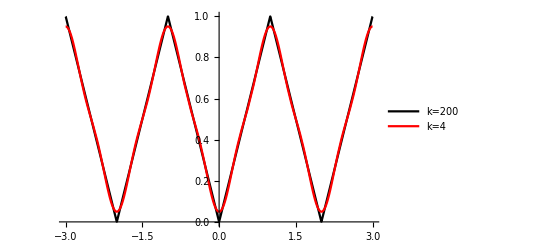

/home/lmackay/Documents/256/2022W1/LM Notes/images/triangle_series.pdf

```mathematica
Plot[Evaluate[{ser2200,ser24 }],{x,-3,3},PlotStyle->{Black,Red},PlotLegends->{"k=200","k=4"}]
Export[NotebookDirectory[]<>"triangle_series.pdf",%]
```

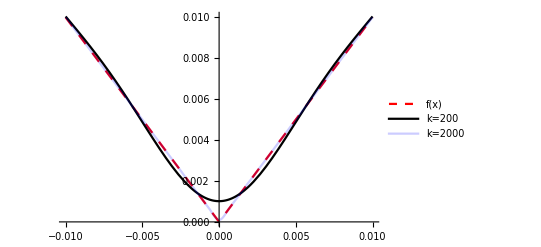

/home/lmackay/Documents/256/2022W1/LM Notes/images/triangle_zoom_in.pdf

```mathematica
Plot[{Abs[x],ser2200, ser22000},{x,-.01,.01},PlotStyle->{Directive[Red,Dashing[{.02,.02}]],Black, Directive[Thick,Blue, Opacity[.2]]},PlotLegends->{"f(x)","k=200","k=2000"}]
Export[NotebookDirectory[]<>"triangle_zoom_in.pdf",%]
```